```mathematica
Exit
```

#### Upload an image

```mathematica
image = Image[Import["https://upload.wikimedia.org/wikipedia/commons/thumb/9/9f/Gabriel_graph.svg/1200px-Gabriel_graph.svg.png"],ImageSize->600]
```

-Graphics-

```mathematica
Show[image,GraphPlot[MorphologicalGraph[Dilation[AlphaChannel[image],1]]]]
```

-Graphics-

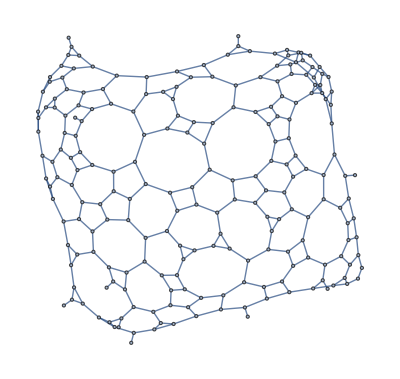

```mathematica
CanonicalGraph[MorphologicalGraph[Dilation[AlphaChannel[image],1]]]
```

#### Get dominant colors

Dominant colors help me to distinguish the categories of objects.

```mathematica
dominantColors = DominantColors[image]
```

{RGBColor[0.000027949731121614266, 7.898307605508142*^-6, 7.898332015380695*^-6],RGBColor[0.0034074563895403753, 0.32537803497587997, 0.32537760797495413],RGBColor[0.9978443484804592, 0., 2.8519001281783472*^-6]}

```mathematica
n=10^-3
```

1/1000

It seems black color is the edge of every object on the image. 
Let’s try remove it.

#### Select all colors != black

```mathematica
usefulColors = Select[dominantColors, Total [Apply[List,#]] > n & ]
```

{RGBColor[0.0034074563895403753, 0.32537803497587997, 0.32537760797495413],RGBColor[0.9978443484804592, 0., 2.8519001281783472*^-6]}

#### Edges & vertices extraction

{-Graphics-,-Graphics-}

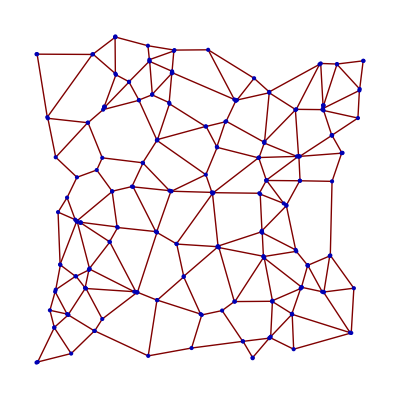

```mathematica
binarized = ChanVeseBinarize[image, #]& /@usefulColors
```

```mathematica
MorphologicalEulerNumber[%]
```

-112

#### How much edges

```mathematica
MorphologicalEulerNumber[binarized[[1]]]
```

186

#### How much vertices

```mathematica
MorphologicalEulerNumber[binarized[[2]]]
```

100

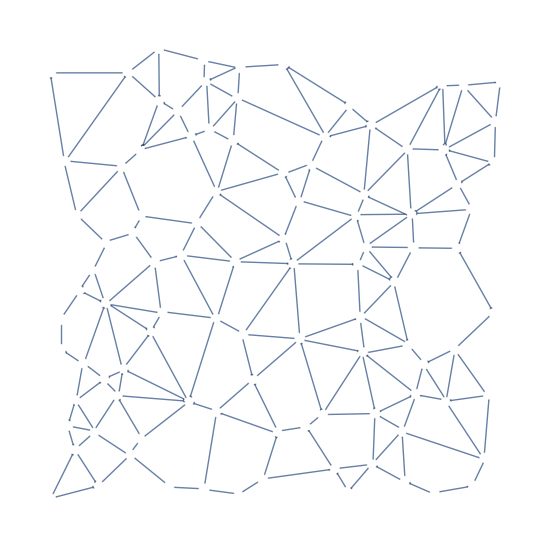

```mathematica
MorphologicalGraph[binarized[[1]]]
```

```mathematica
EdgeDetect[-Graphics-] //FullForm
```

Image[RawArray["UnsignedInteger8",List[1]],"Bit",Rule[ColorSpace,Automatic],Rule[Interleaving,None]]
 |  |  |  |

```mathematica
Disk[{308.29881656804736,1161.585798816568},10.37249929043725]∩ Line[{{0.,117.93131088258873},{1200.,918.4806674379237}}]
```

Intersection::heads: Heads Line and Disk at positions 2 and 1 are expected to be the same.

Disk[{308.299,1161.59},10.3725]∩Line[{{0.,117.931},{1200.,918.481}}]

```mathematica
ImageLines[binarized[[1]]] //FullForm
```

List[List[List[0.,117.931],List[1200.,918.481]],List[List[1188.35,1200.],List[98.1703,0.]],List[List[0.,641.875],List[545.706,1200.]],List[List[16.6498,1200.],List[244.319,0.]],List[List[691.825,1200.],List[288.611,0.]],List[List[0.,648.041],List[1200.,606.025]],List[List[0.,561.526],List[1200.,330.748]],List[List[0.,426.149],List[1137.94,0.]],List[List[1200.,9.37672],List[438.269,1200.]],List[List[660.689,1200.],List[14.2045,0.]],List[List[1200.,726.052],List[152.765,1200.]],List[List[0.,107.319],List[1200.,1064.52]],List[List[0.,513.056],List[1200.,113.178]],List[List[443.593,1200.],List[789.732,0.]],List[List[258.547,1200.],List[854.315,0.]],List[List[1200.,1101.06],List[90.652,0.]],List[List[816.781,1200.],List[363.968,0.]],List[List[0.,1128.05],List[323.351,0.]],List[List[1200.,909.158],List[159.884,0.]],List[List[0.,18.4588],List[1200.,167.21]],List[List[0.,543.358],List[1200.,400.694]],List[List[0.,355.71],List[1200.,1003.49]],List[List[352.238,1200.],List[19.0592,0.]],List[List[0.,1013.56],List[1200.,113.904]],List[List[0.,716.169],List[1200.,760.188]],List[List[0.,1140.68],List[1200.,253.453]],List[List[1200.,104.638],List[574.067,1200.]],List[List[1200.,947.852],List[35.7948,0.]],List[List[0.,1118.23],List[1200.,868.729]],List[List[65.4552,1200.],List[719.702,0.]],List[List[0.,473.589],List[947.949,0.]],List[List[0.,310.771],List[1200.,212.554]],List[List[0.,1105.58],List[1200.,1065.56]],List[List[751.273,1200.],List[856.54,0.]],List[List[1200.,34.0789],List[351.423,1200.]],List[List[0.,673.112],List[1200.,1016.]],List[List[853.312,1200.],List[762.14,0.]],List[List[0.,463.206],List[1200.,1185.22]],List[List[694.213,1200.],List[886.838,0.]],List[List[741.928,1200.],List[7.5982,0.]],List[List[1200.,482.6],List[64.1264,1200.]],List[List[1200.,1146.45],List[13.6998,0.]],List[List[589.913,1200.],List[1175.74,0.]],List[List[517.137,1200.],List[425.965,0.]],List[List[1200.,611.073],List[16.2573,1200.]],List[List[0.,774.114],List[298.179,1200.]],List[List[0.,25.8324],List[931.803,1200.]],List[List[1117.,1200.],List[716.008,0.]],List[List[0.,954.17],List[547.362,0.]],List[List[565.456,1200.],List[721.32,0.]],List[List[0.,936.252],List[1200.,272.895]],List[List[0.,693.089],List[1200.,655.077]],List[List[1045.73,1200.],List[205.568,0.]],List[List[0.,558.629],List[1200.,1158.14]],List[List[1200.,1134.49],List[856.309,0.]],List[List[0.,1133.74],List[833.861,0.]],List[List[915.165,1200.],List[978.221,0.]],List[List[1157.12,1200.],List[1118.11,0.]],List[List[0.,1125.95],List[1126.88,0.]],List[List[0.,626.412],List[1056.99,0.]],List[List[0.,219.954],List[1200.,1023.4]],List[List[1200.,220.118],List[384.408,1200.]],List[List[1200.,989.292],List[555.396,0.]],List[List[1200.,937.853],List[151.481,1200.]],List[List[773.83,1200.],List[1013.95,0.]],List[List[1092.17,1200.],List[401.122,0.]],List[List[0.,1135.48],List[1200.,642.229]],List[List[0.,217.595],List[1200.,617.473]],List[List[0.,769.908],List[1200.,641.424]],List[List[1200.,133.1],List[135.764,1200.]],List[List[1200.,186.988],List[5.37343,1200.]],List[List[0.,892.488],List[1200.,731.537]],List[List[0.,202.286],List[1200.,1156.22]],List[List[1200.,78.3506],List[88.5853,1200.]],List[List[1200.,986.138],List[216.324,0.]],List[List[1200.,739.806],List[510.183,1200.]],List[List[943.791,1200.],List[916.787,0.]],List[List[0.,1107.38],List[1200.,79.4487]],List[List[0.,681.318],List[1200.,560.919]],List[List[0.,1095.69],List[1200.,1141.71]],List[List[1200.,1138.31],List[589.194,0.]],List[List[831.667,1200.],List[846.668,0.]],List[List[816.971,1200.],List[6.26657,0.]],List[List[0.,388.915],List[1023.8,1200.]],List[List[308.307,1200.],List[299.307,0.]],List[List[0.,26.8546],List[1200.,369.747]],List[List[631.595,1200.],List[909.398,0.]],List[List[1100.27,1200.],List[799.184,0.]],List[List[897.536,1200.],List[121.324,0.]]]

#### Extract centroids, its center and radius

```mathematica
vertices=ComponentMeasurements[binarized[[2]],{"Centroid","EquivalentDiskRadius"}];
```

```mathematica
vertices
```

{1→{{308.299,1161.59},10.3725},2→{{419.177,1131.79},10.3109},3→{{621.905,1121.82},10.2955},4→{{511.44,1114.78},10.3264},5→{{38.0419,1100.96},10.3109},6→{{231.643,1100.68},10.3418},7→{{425.5,1079.04},10.3725},8→{{1161.98,1078.63},10.3264},9→{{1015.,1071.},10.28},10→{{1070.,1067.},10.28},11→{{504.187,1038.88},10.28},12→{{310.014,1030.97},10.2955},13→{{785.476,1018.98},10.3571},14→{{356.414,1005.7},10.3725},15→{{1149.12,978.377},10.2955},16→{{838.662,970.029},10.2955},17→{{435.075,960.263},10.3109},18→{{389.394,942.565},10.4031},19→{{723.,940.},10.28},20→{{494.797,931.017},10.2955},21→{{928.695,910.556},10.3878},22→{{1021.53,908.771},10.3418},23→{{262.801,906.53},10.3264},24→{{74.2635,880.925},10.3109},25→{{1144.,879.},10.28},26→{{689.741,869.946},10.28},27→{{215.,865.},10.28},28→{{619.929,851.767},10.2955},29→{{1053.2,821.47},10.3264},30→{{451.2,804.341},10.2955},31→{{820.473,795.568},10.3725},32→{{657.203,780.017},10.2955},33→{{1089.67,760.328},10.3571},34→{{939.,748.},10.28},35→{{104.,744.71},10.3109},36→{{262.958,744.042},10.3109},37→{{801.,744.},10.28},38→{{403.568,726.527},10.3725},39→{{244.986,702.029},10.2955},40→{{620.076,685.658},10.3264},41→{{176.5,675.793},10.3109},42→{{826.296,665.874},10.3109},43→{{943.47,664.199},10.3264},44→{{1054.81,662.56},10.3109},45→{{365.68,645.054},10.3109},46→{{298.,628.393},10.3418},47→{{499.233,628.929},10.2955},48→{{643.216,623.955},10.3109},49→{{805.222,622.44},10.3264},50→{{142.929,607.617},10.2955},51→{{897.377,579.875},10.2955},52→{{111.,557.},10.28},53→{{175.105,525.647},10.3109},54→{{316.5,503.298},10.3571},55→{{1144.,502.},10.28},56→{{811.946,490.32},10.3109},57→{{451.446,487.973},10.3418},58→{{66.097,485.715},10.3264},59→{{289.71,454.47},10.3725},60→{{518.26,447.467},10.3571},61→{{661.5,437.207},10.3109},62→{{931.459,421.459},10.3878},63→{{65.1985,409.47},10.3264},64→{{1047.92,409.204},10.3109},65→{{818.79,403.177},10.3109},66→{{119.932,375.941},10.2955},67→{{969.924,373.342},10.3264},68→{{219.687,361.613},10.3571},69→{{172.874,335.551},10.3109},70→{{543.5,334.5},10.4184},71→{{949.422,298.167},10.2955},72→{{1131.,296.229},10.28},73→{{204.627,294.541},10.3725},74→{{101.,284.229},10.28},75→{{384.47,280.229},10.3418},76→{{1024.26,280.075},10.3109},77→{{451.946,254.32},10.3109},78→{{849.47,250.199},10.3264},79→{{717.353,247.895},10.3109},80→{{81.3533,220.895},10.3109},81→{{676.,218.},10.28},82→{{916.121,206.673},10.3264},83→{{147.113,203.095},10.2645},84→{{605.589,202.731},10.3571},85→{{263.042,187.958},10.3109},86→{{98.5,159.298},10.3571},87→{{237.076,147.658},10.3264},88→{{1120.5,138.298},10.3571},89→{{841.084,123.916},10.28},90→{{747.813,111.877},10.28},91→{{567.459,86.6272},10.3725},92→{{923.372,80.6276},10.3571},93→{{1093.17,69.4521},10.3109},94→{{157.054,68.9699},10.28},95→{{335.,68.},10.28},96→{{421.527,61.432},10.3725},97→{{780.342,54.0761},10.3264},98→{{997.145,51.0964},10.28},99→{{506.586,46.2988},10.3725},100→{{38.0285,38.3378},10.2955}}

```mathematica
ImageLines[binarized[[1]]]
```

{{{0.,117.931},{1200.,918.481}},{{1188.35,1200.},{98.1703,0.}},{{0.,641.875},{545.706,1200.}},{{16.6498,1200.},{244.319,0.}},{{691.825,1200.},{288.611,0.}},{{0.,648.041},{1200.,606.025}},{{0.,561.526},{1200.,330.748}},{{0.,426.149},{1137.94,0.}},{{1200.,9.37672},{438.269,1200.}},{{660.689,1200.},{14.2045,0.}},{{1200.,726.052},{152.765,1200.}},{{0.,107.319},{1200.,1064.52}},{{0.,513.056},{1200.,113.178}},{{444.668,1200.},{788.642,0.}},{{258.547,1200.},{854.315,0.}},{{1200.,1101.06},{90.652,0.}},{{816.781,1200.},{363.968,0.}},{{0.,1128.05},{323.351,0.}},{{1200.,909.158},{159.884,0.}},{{0.,18.4588},{1200.,167.21}},{{0.,543.358},{1200.,400.694}},{{0.,355.71},{1200.,1003.49}},{{352.238,1200.},{19.0592,0.}},{{0.,1013.56},{1200.,113.904}},{{0.,716.169},{1200.,760.188}},{{0.,1140.68},{1200.,253.453}},{{1200.,104.638},{574.067,1200.}},{{1200.,947.852},{35.7948,0.}},{{0.,1118.23},{1200.,868.729}},{{65.4552,1200.},{719.702,0.}},{{0.,473.589},{947.949,0.}},{{0.,310.771},{1200.,212.554}},{{0.,1105.58},{1200.,1065.56}},{{751.273,1200.},{856.54,0.}},{{1200.,34.0789},{351.423,1200.}},{{0.,673.112},{1200.,1016.}},{{853.312,1200.},{762.14,0.}},{{0.,463.206},{1200.,1185.22}},{{694.213,1200.},{886.838,0.}},{{741.928,1200.},{7.5982,0.}},{{1200.,482.6},{64.1264,1200.}},{{1200.,1146.45},{13.6998,0.}},{{589.913,1200.},{1175.74,0.}},{{516.162,1200.},{429.011,0.}},{{1200.,611.073},{16.2573,1200.}},{{0.,774.114},{298.179,1200.}},{{0.,25.8324},{931.803,1200.}},{{1117.,1200.},{716.008,0.}},{{0.,954.17},{547.362,0.}},{{565.456,1200.},{721.32,0.}},{{0.,936.252},{1200.,272.895}},{{0.,693.089},{1200.,655.077}},{{1045.73,1200.},{205.568,0.}},{{0.,558.629},{1200.,1158.14}},{{1200.,1134.49},{856.309,0.}},{{0.,1133.74},{833.861,0.}},{{915.165,1200.},{978.221,0.}},{{1157.12,1200.},{1118.11,0.}},{{0.,1125.95},{1126.88,0.}},{{0.,626.412},{1056.99,0.}},{{0.,219.954},{1200.,1023.4}},{{1200.,220.118},{384.408,1200.}},{{1200.,989.292},{555.396,0.}},{{1200.,937.853},{151.481,1200.}},{{1092.17,1200.},{401.122,0.}},{{773.83,1200.},{1013.95,0.}},{{0.,1135.48},{1200.,642.229}},{{0.,217.595},{1200.,617.473}},{{0.,769.908},{1200.,641.424}},{{1200.,133.1},{135.764,1200.}},{{1200.,186.988},{5.37343,1200.}},{{0.,892.488},{1200.,731.537}},{{0.,202.286},{1200.,1156.22}},{{1200.,78.3506},{88.5853,1200.}},{{1200.,986.138},{216.324,0.}},{{1200.,739.806},{510.183,1200.}},{{943.791,1200.},{916.787,0.}},{{0.,1107.38},{1200.,79.4487}},{{0.,681.318},{1200.,560.919}},{{0.,1095.69},{1200.,1141.71}},{{1200.,1138.31},{589.194,0.}},{{831.667,1200.},{846.668,0.}},{{816.971,1200.},{6.26657,0.}},{{0.,388.915},{1023.8,1200.}},{{308.307,1200.},{299.307,0.}},{{0.,26.8546},{1200.,369.747}},{{631.595,1200.},{909.398,0.}},{{1100.27,1200.},{799.184,0.}},{{897.536,1200.},{121.324,0.}}}

```mathematica
(Disk @@@ Values[vertices])[[1]]
```

Disk[{308.299,1161.59},10.3725]

```mathematica
{308.29881656804736,1161.585798816568}∈Disk[{308.29881656804736,1161.585798816568},10.37249929043725]
```

True

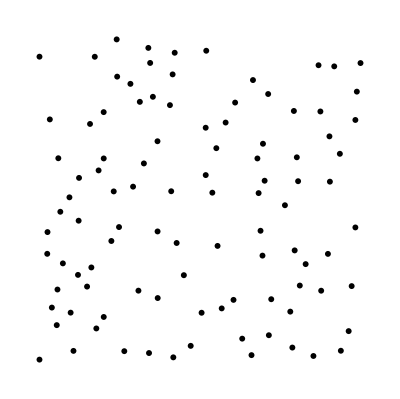

```mathematica
Graphics[Disk @@@ Values[vertices]]
```

```mathematica
Graphics[Disk /@ Values[vertices]]
```

#### Lines extraction

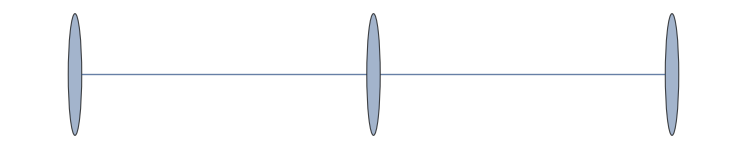

```mathematica
RandomGraph[{3,2}]
```

```mathematica
img2 = Import["https://upload.wikimedia.org/wikipedia/commons/thumb/0/06/Heawood_Graph.svg/1200px-Heawood_Graph.svg.png"];
```

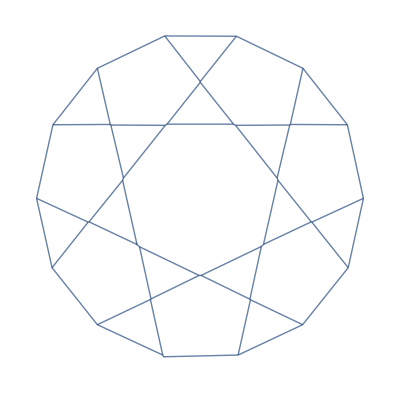

```mathematica
MorphologicalGraph[ColorNegate[img2]]
```

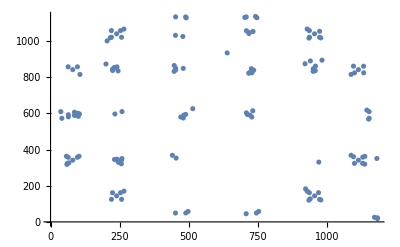

```mathematica
ListPlot[ImageKeypoints[img2]]
```

```mathematica
ComponentMeasurements[]
```

```mathematica
SelectComponents[img2, {"Image", "Count", "Mean"}, All, "Dataset" ]
```

-Graphics-

```mathematica
SelectComponents[-Graphics-,]
```

SelectComponents::invtest2: Cannot infer any known component property from the test function Circularity.

SelectComponents[-Graphics-,Circularity]